# Vaje iz Mathematice

Rešuj naloge v celicah med navodili. Pomagaj si z gradivom na spletni učilnici.

1. naloga: Izračunaj vrednost izraza ((20 +316)^7-55)/(33 12)^3. Izračunaj tudi numerično vrednost izraza na 20 mest natančno.

```mathematica
N[((20 +316)^7-55)/(33 12)^3,20 ]
```

7.7855515381036805568×10^9

2. naloga: Poenostavi izraz 2^x+5 a 2^x+2^(x+2). Pomagaj si z ukazom Simplify.

```mathematica
Simplify[2^x+5 a 2^x+2^(x+2)]
```

5 2^x (1+a)

3. naloga: Izračunaj 30! - 20!. Kakšna je 10 števka od leve proti desni? Razcepi rezultat na prafaktorje. Katero je največje praštevilo v razcepu? Katero praštevilo nastopa v razcepu z najvišjo potenco.

```mathematica
khm = Evaluate[30! - 20!]
```

265252859812188625734300303360000

```mathematica
IntegerDigits[khm][[10]]
```

8

```mathematica
FactorInteger[khm]
```

{{2,18},{3,8},{5,4},{7,2},{11,1},{13,1},{17,1},{19,1},{124669,1},{874534571,1}}

```mathematica
(* izraz /. x-->1  ; zamenja vse x-e v izrazu z 1 *)
```

18

4. naloga: Poišči največji skupni delitelj in najmanjši skupni večkratnik števil: 536, 1248, 2320.

```mathematica
GCD[536,1248,2320]
```

8

```mathematica
LCM[536,1248,2320]
```

12124320

5. naloga: Izračunaj vrednost izraza (x^5- 2 x^2+3x + 4)/(x^5-2x - 1) pri x = 1, 2, 3, 4. Uporabi ustrezna transformacijska pravila in ukaz ReplaceAll (oz /.)

```mathematica
a=(x^5- 2 x^2+3x + 4)/(x^5-2x - 1)
Solve[ReplaceAll[x->{1,2,3,4}][a]]
```

(4+3 x-2 x^2+x^5)/(-1-2 x+x^5)

Solve::naqs: -3&&34/27&&119/118&&-3 is not a quantified system of equations and inequalities.

Solve[{-3,34/27,119/118,-3}]

```mathematica
Table[a,{x,1,4}]
```

{-3,34/27,119/118,144/145}

6. naloga: Napiši funkcijo odvisno od x, katere vrednost je ravno izraz iz prejšnje naloge. S pomočjo ukaza Table izračunaj vrednosti funkcije v točkah od 1 do 10.

```mathematica
f[x_]:=a
Table[f[x],{x,1,10}]
```

{-3,34/27,119/118,144/145,1547/1557,7726/7763,8367/8396,32668/32751,29459/29515,99834/99979}

7. naloga: Izračunaj naslednje limite:
	lim_(x→ 2) (x^3- 4 x^2+2x + 4)/(x^5-9x - 14)
	lim_(x→ 0) (arctan(7x))/(arcsin(8x))
	lim_(x→ 5) (x^2-25)cot(πx)
	lim_(x→ π) (1 + cos x)/(2 √πx- π - x)
	lim_(x→ 0^+) |x| cot x
lim_(x→ 0^-) |x| cot x

```mathematica
Evaluate[lim_(x-> 2) (x^3- 4 x^2+2x + 4)/(x^5-9x - 14)]
```

-2/71

```mathematica
Limit[(x^3- 4 x^2+2x + 4)/(x^5-9x - 14),x->2]
```

-2/71

```mathematica
Limit[Abs[x]*Cot[x],x->0,Direction->"FromBelow"]
```

-1

```mathematica
Limit[ArcTan[7x]/ArcSin[8x],x->0]
```

7/8

8. naloga: Izračunaj odvode naslednjih funkcij:
	y = (arctan(x))/(arcsin(x))
	y = (((x^3 + 1)^(1/3) + 5)/(4 (x^3+1)^(1/3)+2))^(2/5)
	y = √((x^2 + 1)^(1/3) +(x^2 + 1)^(1/4))  
	y = (x + 1)^x

```mathematica
D[(arctan(x))/(arcsin(x)),x]
```

-(arctan x)/(√(1-x^2) ArcSin[x]^2)+arctan/ArcSin[x]

```mathematica
D[(((x^3 + 1)^(1/3) + 5)/(4 (x^3+1)^(1/3)+2))^(2/5),x]
```

(2 (-(4 x^2 (5+(1+x^3)^(1/3)))/((1+x^3)^(2/3) (2+4 (1+x^3)^(1/3))^2)+x^2/((1+x^3)^(2/3) (2+4 (1+x^3)^(1/3)))))/(5 ((5+(1+x^3)^(1/3))/(2+4 (1+x^3)^(1/3)))^(3/5))

```mathematica
D[(x + 1)^x,x]
```

(1+x)^x (x/(1+x)+Log[1+x])

9. naloga: Seštej vsa soda števila na intervalu od [1, 100].

```mathematica
Sum[x,{x,2,100,2}]
Sum[2i,{i,1,50}]
```

2550

2550

10. naloga: Izračunaj ∑_(k=1)^∞ (k^2+1)/k^4.

```mathematica
a = (k^2 + 1)/k^4;
Sum[(k^2 + 1)/k^4,{k,1,Infinity}]
```

1/90 π^2 (15+π^2)

11. naloga: S pomočjo implicitnega odvajanja izračunaj odvode y'(x). Za prvi primer si oglej zgled spodaj.
	cos√xy= x^2 y^2+ 1 
	1 + sin(xy) = tan(x + y)
	tan^2(x + y)= x^2y^2 - 3

```mathematica
odvod  = D[Cos[Sqrt[x y[x]]]== x^2 (y[x])^2 + 1,  x]
resitev =First[Solve[odvod, y'[x]]]
y'[x] /. resitev
```

-(Sin[√(x y[x])] (y[x]+x y'[x]))/(2 √(x y[x]))==2 x y[x]^2+2 x^2 y[x] y'[x]

{y'[x]→-y[x]/x}

-y[x]/x

12. naloga: Eksaktno izračunaj ničle polinoma  -1+2 x-7 x^2+x.

```mathematica
Solve[-1+2 x-7 x^2+x^3 == 0,x]
```

{{x→1/3 (7+(587/2-(3 √2949)/2)^(1/3)+(1/2 (587+3 √2949))^(1/3))},{x→7/3-1/6 (1+ⅈ √3) (587/2-(3 √2949)/2)^(1/3)-1/6 (1-ⅈ √3) (1/2 (587+3 √2949))^(1/3)},{x→7/3-1/6 (1-ⅈ √3) (587/2-(3 √2949)/2)^(1/3)-1/6 (1+ⅈ √3) (1/2 (587+3 √2949))^(1/3)}}

13. naloga: Numerično izračunaj ničle polinoma 1-x+12 x^2-2 x^4+x^5. Koliko ničel je realnih? Kakšna je največja absolutna vrednost ničle. S pomočjo ukaza ReplaceAll  (oz. /.) uporabi seznam rešitev na simbolu x. Tako dobiš seznam vrednosti ničel. Nato s pomočjo ukaza Table, ukaza Part (oz [[  ]]) in ukaza Abs sestavi seznam absolutnih vrednosti. Na koncu na seznamu uporabi še funkcijo Max, ki vrne maksimum seznama.

```mathematica
resitev = N[Solve[ 1-x+12 x^2-2 x^4+x^5==0,x]];
N[Solve[ 1-x+12 x^2-2 x^4+x^5==0,x,Reals]];
nicle = x/.resitev
absolutne= Table[Abs[nicle[[i]]],{i,1,5}]
Max[absolutne]
```

{-1.83104,0.0403843-0.284163 ⅈ,0.0403843+0.284163 ⅈ,1.87514-1.76448 ⅈ,1.87514+1.76448 ⅈ}

{1.83104,0.287018,0.287018,2.57479,2.57479}

2.57479

14. naloga: Razcepi polinom na linearne in kvadratne faktorje -1056+256 x-826 x^2+175 x^3+232 x^4-80 x^5+2 x^6+x^7.

```mathematica
Factor[-1056+256 x-826 x^2+175 x^3+232 x^4-80 x^5+2 x^6+x^7]
```

(-4+x)^2 (-3+x) (2+x) (11+x) (1+x^2)

15. naloga: Zmnoži polinom tako da dobiš vsoto monomov (x^2 (-1+y)-x^3 y^5+(-1+x)^7 x y (x^2+2 x y+y^3))^2.  Nato razvij polinom po potencah x (koeficienti so polinomi v y). Ugotovi najvišjo potenco n spremenljivke x, ki se pojavi v polinomu in izračunaj n-ti odvod polinoma.

```mathematica
p =Expand[(x^2 (-1+y)-x^3 y^5+(-1+x)^7 x y (x^2+2 x y+y^3))^2];
```

```mathematica
Collect[p,x]
```

x^20 ((1+x^2)^(1/4)+(1+x^2)^(1/3))+x^2 (1+4 (1+x^2)^(1/12)+6 (1+x^2)^(1/6)+4 (1+x^2)^(1/4)+(1+x^2)^(1/3))+x^19 (4-14 (1+x^2)^(1/4)-14 (1+x^2)^(1/3)+4 (1+x^2)^(1/4) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+4 (1+x^2)^(1/3) √((1+x^2)^(1/4)+(1+x^2)^(1/3)))+x^13 (13606-9464 (1+x^2)^(1/12)-14196 (1+x^2)^(1/6)-12896 (1+x^2)^(1/4)-5798 (1+x^2)^(1/3)-8008 √(1+x^2)-16016 (1+x^2)^(7/12)-8008 (1+x^2)^(2/3)+4002 (1+x^2)^(3/4)+12006 (1+x^2)^(5/6)+12006 (1+x^2)^(11/12)+26 √((1+x^2)^(1/4)+(1+x^2)^(1/3))-8 (1+x^2)^(1/12) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-12 (1+x^2)^(1/6) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+12004 (1+x^2)^(1/4) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+12010 (1+x^2)^(1/3) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-4004 √(1+x^2) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-8008 (1+x^2)^(7/12) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-4004 (1+x^2)^(2/3) √((1+x^2)^(1/4)+(1+x^2)^(1/3)))+x^15 (3988-1512 (1+x^2)^(1/12)-2268 (1+x^2)^(1/6)-3514 (1+x^2)^(1/4)-2380 (1+x^2)^(1/3)-1456 √(1+x^2)-2912 (1+x^2)^(7/12)-1456 (1+x^2)^(2/3)+364 (1+x^2)^(3/4)+1092 (1+x^2)^(5/6)+1092 (1+x^2)^(11/12)+4004 (1+x^2)^(1/4) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+4004 (1+x^2)^(1/3) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-728 √(1+x^2) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-1456 (1+x^2)^(7/12) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-728 (1+x^2)^(2/3) √((1+x^2)^(1/4)+(1+x^2)^(1/3)))+x^17 (354-56 (1+x^2)^(1/12)-84 (1+x^2)^(1/6)-420 (1+x^2)^(1/4)-378 (1+x^2)^(1/3)-56 √(1+x^2)-112 (1+x^2)^(7/12)-56 (1+x^2)^(2/3)+4 (1+x^2)^(3/4)+12 (1+x^2)^(5/6)+12 (1+x^2)^(11/12)+364 (1+x^2)^(1/4) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+364 (1+x^2)^(1/3) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-28 √(1+x^2) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-56 (1+x^2)^(7/12) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-28 (1+x^2)^(2/3) √((1+x^2)^(1/4)+(1+x^2)^(1/3)))+x^3 (-10-56 (1+x^2)^(1/12)-84 (1+x^2)^(1/6)-56 (1+x^2)^(1/4)-14 (1+x^2)^(1/3)+2 √(1+x^2)+4 (1+x^2)^(7/12)+2 (1+x^2)^(2/3)+4 (1+x^2)^(3/4)+12 (1+x^2)^(5/6)+12 (1+x^2)^(11/12)-2 √(1+x^2) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-4 (1+x^2)^(7/12) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-2 (1+x^2)^(2/3) √((1+x^2)^(1/4)+(1+x^2)^(1/3)))+x^18 (-55+4 (1+x^2)^(1/12)+6 (1+x^2)^(1/6)+95 (1+x^2)^(1/4)+92 (1+x^2)^(1/3)+4 √(1+x^2)+8 (1+x^2)^(7/12)+4 (1+x^2)^(2/3)-56 (1+x^2)^(1/4) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-56 (1+x^2)^(1/3) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+2 √(1+x^2) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+4 (1+x^2)^(7/12) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+2 (1+x^2)^(2/3) √((1+x^2)^(1/4)+(1+x^2)^(1/3)))+x^4 (37+368 (1+x^2)^(1/12)+552 (1+x^2)^(1/6)+373 (1+x^2)^(1/4)+97 (1+x^2)^(1/3)-10 √(1+x^2)-20 (1+x^2)^(7/12)-10 (1+x^2)^(2/3)-56 (1+x^2)^(3/4)-168 (1+x^2)^(5/6)-168 (1+x^2)^(11/12)+8 (1+x^2)^(1/12) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+12 (1+x^2)^(1/6) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+4 (1+x^2)^(1/4) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-2 (1+x^2)^(1/3) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+16 √(1+x^2) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+32 (1+x^2)^(7/12) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+16 (1+x^2)^(2/3) √((1+x^2)^(1/4)+(1+x^2)^(1/3)))+x^16 (-1420+368 (1+x^2)^(1/12)+552 (1+x^2)^(1/6)+1369 (1+x^2)^(1/4)+1093 (1+x^2)^(1/3)+364 √(1+x^2)+728 (1+x^2)^(7/12)+364 (1+x^2)^(2/3)-56 (1+x^2)^(3/4)-168 (1+x^2)^(5/6)-168 (1+x^2)^(11/12)-1456 (1+x^2)^(1/4) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-1456 (1+x^2)^(1/3) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+182 √(1+x^2) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+364 (1+x^2)^(7/12) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+182 (1+x^2)^(2/3) √((1+x^2)^(1/4)+(1+x^2)^(1/3)))+x^14 (-8358+4368 (1+x^2)^(1/12)+6552 (1+x^2)^(1/6)+7371 (1+x^2)^(1/4)+4095 (1+x^2)^(1/3)+4004 √(1+x^2)+8008 (1+x^2)^(7/12)+4004 (1+x^2)^(2/3)-1456 (1+x^2)^(3/4)-4368 (1+x^2)^(5/6)-4368 (1+x^2)^(11/12)-4 √((1+x^2)^(1/4)+(1+x^2)^(1/3))-8008 (1+x^2)^(1/4) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-8008 (1+x^2)^(1/3) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+2002 √(1+x^2) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+4004 (1+x^2)^(7/12) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+2002 (1+x^2)^(2/3) √((1+x^2)^(1/4)+(1+x^2)^(1/3)))+x^8 (-5416+16016 (1+x^2)^(1/12)+24024 (1+x^2)^(1/6)+16318 (1+x^2)^(1/4)+4310 (1+x^2)^(1/3)+10 (1+x^2)^(5/12)+3972 √(1+x^2)+7929 (1+x^2)^(7/12)+3963 (1+x^2)^(2/3)-7966 (1+x^2)^(3/4)-23898 (1+x^2)^(5/6)-23898 (1+x^2)^(11/12)-126 √((1+x^2)^(1/4)+(1+x^2)^(1/3))+448 (1+x^2)^(1/12) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+672 (1+x^2)^(1/6) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-1148 (1+x^2)^(1/4) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-1484 (1+x^2)^(1/3) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+2044 √(1+x^2) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+4088 (1+x^2)^(7/12) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+2044 (1+x^2)^(2/3) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-140 (1+x^2)^(3/4) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-420 (1+x^2)^(5/6) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-420 (1+x^2)^(11/12) √((1+x^2)^(1/4)+(1+x^2)^(1/3)))+x^10 (-15618+24024 (1+x^2)^(1/12)+36036 (1+x^2)^(1/6)+25095 (1+x^2)^(1/4)+7077 (1+x^2)^(1/3)+12010 √(1+x^2)+24020 (1+x^2)^(7/12)+12010 (1+x^2)^(2/3)-13658 (1+x^2)^(3/4)-40974 (1+x^2)^(5/6)-40974 (1+x^2)^(11/12)-182 √((1+x^2)^(1/4)+(1+x^2)^(1/3))+336 (1+x^2)^(1/12) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+504 (1+x^2)^(1/6) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-7700 (1+x^2)^(1/4) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-7952 (1+x^2)^(1/3) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+6008 √(1+x^2) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+12016 (1+x^2)^(7/12) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+6008 (1+x^2)^(2/3) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-84 (1+x^2)^(3/4) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-252 (1+x^2)^(5/6) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-252 (1+x^2)^(11/12) √((1+x^2)^(1/4)+(1+x^2)^(1/3)))+x^6 (-418+4368 (1+x^2)^(1/12)+6552 (1+x^2)^(1/6)+4468 (1+x^2)^(1/4)+1196 (1+x^2)^(1/3)+10 (1+x^2)^(5/12)+304 √(1+x^2)+593 (1+x^2)^(7/12)+295 (1+x^2)^(2/3)-1454 (1+x^2)^(3/4)-4362 (1+x^2)^(5/6)-4362 (1+x^2)^(11/12)+2 √((1+x^2)^(1/4)+(1+x^2)^(1/3))+176 (1+x^2)^(1/12) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+264 (1+x^2)^(1/6) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+36 (1+x^2)^(1/4) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-96 (1+x^2)^(1/3) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+252 √(1+x^2) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+504 (1+x^2)^(7/12) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+252 (1+x^2)^(2/3) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-28 (1+x^2)^(3/4) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-84 (1+x^2)^(5/6) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-84 (1+x^2)^(11/12) √((1+x^2)^(1/4)+(1+x^2)^(1/3)))+x^12 (-17648+16016 (1+x^2)^(1/12)+24024 (1+x^2)^(1/6)+19021 (1+x^2)^(1/4)+7009 (1+x^2)^(1/3)+12012 √(1+x^2)+24024 (1+x^2)^(7/12)+12012 (1+x^2)^(2/3)-7994 (1+x^2)^(3/4)-23982 (1+x^2)^(5/6)-23982 (1+x^2)^(11/12)-76 √((1+x^2)^(1/4)+(1+x^2)^(1/3))+56 (1+x^2)^(1/12) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+84 (1+x^2)^(1/6) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-13672 (1+x^2)^(1/4) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-13714 (1+x^2)^(1/3) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+6006 √(1+x^2) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+12012 (1+x^2)^(7/12) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+6006 (1+x^2)^(2/3) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-4 (1+x^2)^(3/4) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-12 (1+x^2)^(5/6) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-12 (1+x^2)^(11/12) √((1+x^2)^(1/4)+(1+x^2)^(1/3)))+x^5 (-12-1512 (1+x^2)^(1/12)-2268 (1+x^2)^(1/6)-1542 (1+x^2)^(1/4)-408 (1+x^2)^(1/3)-14 √(1+x^2)-28 (1+x^2)^(7/12)-14 (1+x^2)^(2/3)+362 (1+x^2)^(3/4)+1086 (1+x^2)^(5/6)+1086 (1+x^2)^(11/12)-8 √((1+x^2)^(1/4)+(1+x^2)^(1/3))-56 (1+x^2)^(1/12) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-84 (1+x^2)^(1/6) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-24 (1+x^2)^(1/4) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+18 (1+x^2)^(1/3) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-68 √(1+x^2) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-136 (1+x^2)^(7/12) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-68 (1+x^2)^(2/3) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+4 (1+x^2)^(3/4) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+12 (1+x^2)^(5/6) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+12 (1+x^2)^(11/12) √((1+x^2)^(1/4)+(1+x^2)^(1/3)))+x^11 (18478-21736 (1+x^2)^(1/12)-32604 (1+x^2)^(1/6)-23756 (1+x^2)^(1/4)-7454 (1+x^2)^(1/3)-13728 √(1+x^2)-27456 (1+x^2)^(7/12)-13728 (1+x^2)^(2/3)+11970 (1+x^2)^(3/4)+35910 (1+x^2)^(5/6)+35910 (1+x^2)^(11/12)+138 √((1+x^2)^(1/4)+(1+x^2)^(1/3))-176 (1+x^2)^(1/12) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-264 (1+x^2)^(1/6) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+11840 (1+x^2)^(1/4) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+11972 (1+x^2)^(1/3) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-6864 √(1+x^2) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-13728 (1+x^2)^(7/12) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-6864 (1+x^2)^(2/3) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+28 (1+x^2)^(3/4) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+84 (1+x^2)^(5/6) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+84 (1+x^2)^(11/12) √((1+x^2)^(1/4)+(1+x^2)^(1/3)))+x^7 (1986-9464 (1+x^2)^(1/12)-14196 (1+x^2)^(1/6)-9660 (1+x^2)^(1/4)-2562 (1+x^2)^(1/3)-1386 √(1+x^2)-2772 (1+x^2)^(7/12)-1386 (1+x^2)^(2/3)+3990 (1+x^2)^(3/4)+11970 (1+x^2)^(5/6)+11970 (1+x^2)^(11/12)+46 √((1+x^2)^(1/4)+(1+x^2)^(1/3))-336 (1+x^2)^(1/12) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-504 (1+x^2)^(1/6) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+168 (1+x^2)^(1/4) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+420 (1+x^2)^(1/3) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-798 √(1+x^2) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-1596 (1+x^2)^(7/12) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-798 (1+x^2)^(2/3) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+84 (1+x^2)^(3/4) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+252 (1+x^2)^(5/6) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+252 (1+x^2)^(11/12) √((1+x^2)^(1/4)+(1+x^2)^(1/3)))+x^9 (10498-21736 (1+x^2)^(1/12)-32604 (1+x^2)^(1/6)-22254 (1+x^2)^(1/4)-5952 (1+x^2)^(1/3)-7994 √(1+x^2)-15988 (1+x^2)^(7/12)-7994 (1+x^2)^(2/3)+11942 (1+x^2)^(3/4)+35826 (1+x^2)^(5/6)+35826 (1+x^2)^(11/12)+182 √((1+x^2)^(1/4)+(1+x^2)^(1/3))-448 (1+x^2)^(1/12) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-672 (1+x^2)^(1/6) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+3640 (1+x^2)^(1/4) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+3976 (1+x^2)^(1/3) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-4018 √(1+x^2) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-8036 (1+x^2)^(7/12) √((1+x^2)^(1/4)+(1+x^2)^(1/3))-4018 (1+x^2)^(2/3) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+140 (1+x^2)^(3/4) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+420 (1+x^2)^(5/6) √((1+x^2)^(1/4)+(1+x^2)^(1/3))+420 (1+x^2)^(11/12) √((1+x^2)^(1/4)+(1+x^2)^(1/3)))

```mathematica
D[p,{x,20}]
```

16. naloga: Nariši graf funkcije y = (x^2 - 1)/(x^2- 4). Računsko pa pri tem določi (in se potem s sliko prepričaj) naslednje:
- ničle funkcije
- pole funkcije in obnašanje funkcije v okolicah polov
- asimptote
- ekstreme 
- prevoje
- intervale konveksnosti in konkavnosti
Rezultate naloge komentiraj z vmesnimi tekstovnimi celicami.

17. naloga: Analiziraj funkcijo y = arctanx^2/(x^2-1). Upoštevaj navodila iz prejšnje naloge.

18. naloga: Določi tangento na funkcijo y=sin^2 x-cos x v točki (2,y[2]). Rezultat predstavi s sliko.

```mathematica
f[x_]=(Sin[x])^2 - Cos[x]
y[x_]=f'[2]x+f[2]-f'[2]2
```

-Cos[x]+Sin[x]^2

-Cos[2]+Sin[2]^2-2 (Sin[2]+2 Cos[2] Sin[2])+x (Sin[2]+2 Cos[2] Sin[2])

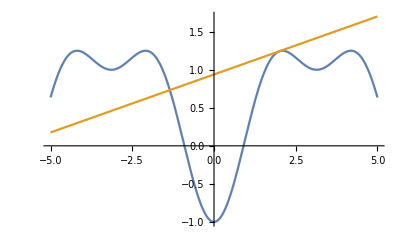

```mathematica
Plot[{f[x],y[x]},{x,-5,5}]
```

19. naloga: Dana sta vektorja v1 = (1,2,3) in v2 = (-3,-2,5). Izračunaj njun skalarni produkt ter vektorski produkt. Kateri od vektorjev je daljši. Sestavi enačbo ravnine, ki gre skozi točko (1,1,1) in ima normalo v smeri vektorskega produkta.

Izračunaj determinanto matrike.
M = (9 | 2 | -3
3 | 2 | 1
6 | 4 | -1)
Izračunaj tudi lastne vrednosti in lastne vektorje matrike M. Ali je matrika diagonalizabilna? Konstruiraj diagonalno matriko, prehodno matriko in njen inverz. Preveri, če produkt teh treh matrik da spet matriko M.

```mathematica
v1 ={1,2,3};
v2 = {-3,-2,5};

v1.v2
Cross[v1,v2]
```

8

{16,-14,4}

```mathematica
Norm[v1]
Norm[v2]
```

√14

20. naloga: Dana je parametrično podana krivulja (((3-t) sin t)/(1+t),cos(t) sin(2 t)) za t ∈ [0,5]. Krivulja samo sebe preseka natanko dvakrat. S pomočjo numeričnega reševanja enačb (FindRoot) poišči približka koordinat točk. Sistem enačb nastavi tako da izenačiš par koordinat krivulj prametriziran s t s parom parametriziranim s spremenljivko s. Potem s spreminjanjem začetnih približkov poskusi določiti vrednosti parametra, pri katerih pride do samopresečič. Ko izračunaš točke p1, p2, ..., sestavi iz njih grafični objekt Graphics[{Point[p1], Point[p2], ...}] in ga z ukazom Show prikaži skupaj s sliko, ki jo pridela ukaz ParametricPlot. S tem grafično preveri, če gre za pravilen izračun.

21. naloga: S simboličnim računom dokaži identiteto a × (b × c) = b(a · c) − c(a · b) na trorazsežnih vektorjih.

```mathematica
a = {a1,a2,a3};
b = {b1,b2,b3};
c ={c1,c2,c3};
```

```mathematica
Cross[a,Cross[b,c]]== b(a.c)-c(a.b)//Simplify
```

True